time: 4. μs

using a time step of 0.002μs

chirp step: 0.

0.00011

1.07368

1.01717

-2.15236×10^6

power broadening :0.0000228537

resonance defect :0.00011

ratio: 1 to4.81322

2.15236×10^6

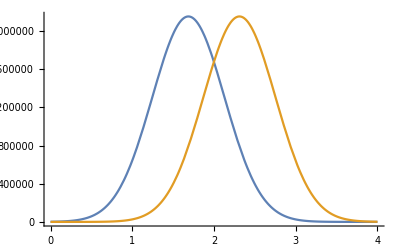

Η[2.]

-0.536841 | 0. | -1.07618×10^6 | 1.07618×10^6 | 0. | 0.
0. | 0.536841 | 1.07618×10^6 | 1.07618×10^6 | 0. | 0.
-1.07618×10^6 | 1.07618×10^6 | 0. | 0. | 395905. | -395905.
1.07618×10^6 | 1.07618×10^6 | 0. | 2.07202×10^7 | 395905. | 395905.
0. | 0. | 395905. | 395905. | -0.508586 | 0.
0. | 0. | -395905. | 395905. | 0. | 0.508586

{0.270395,Null}

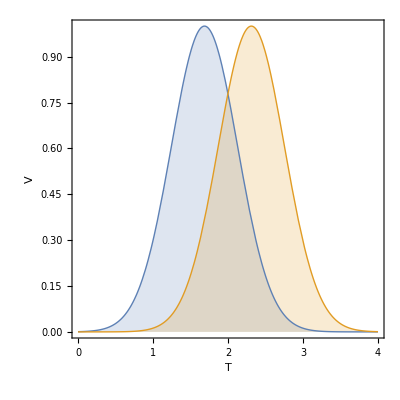

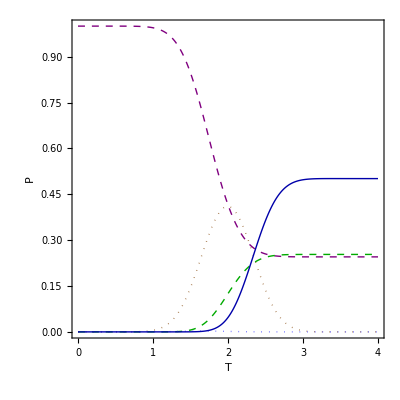

last state vector: {0.493344+0.0437017 ⅈ,0.501422+0.0437004 ⅈ,-8.85629×10^-8-0.00842552 ⅈ,0.0000182925-0.0000292969 ⅈ,0.49847+0.0264214 ⅈ,-0.501426+0.0264205 ⅈ}

last population: {0.245299,0.253334,0.0000709894,1.19292×10^-9,0.249171,0.252126}

final norm: 1.

{0.496596+0.0264007 ⅈ,-0.499497+0.0263997 ⅈ}

{0.247304,0.250194}

populations in λ, ρ: 0.497498

b+ -0.00205145-0.0373355 ⅈ

b- 0.704344-6.82294×10^-7 ⅈ

parity of superposition χ+: 0.00139815 χ-: 0.4961

1.

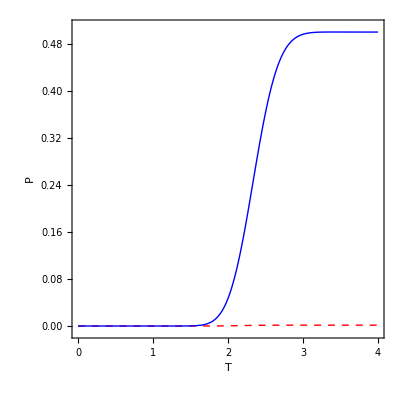

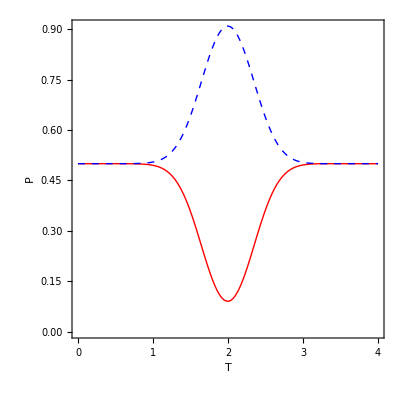

```mathematica
ClearAll["`*"];
(* Calculates a STIRAP transition for Cl2O2 *)
NT = 2001;
dt =0.002 ;
sq2=Sqrt[2.];
ℏ=10^6; (* account for the Hamiltonian given in 1/μs *)
Print["time: ", (NT-1)*dt, " μs"]
Print["using a time step of ", dt, "μs"]
(*
(* Molecular Parameters *)
Δ1=2π* 2. 10^3; (* ca. 7. 10^-8 cm^-1 *)
Δ2=2π* 100. 10^6; (* ca. 3. 10^-3 cm^-1 *)
Δ3=2π* 0.5 10^3; (* ca. 1.7 10^-8 cm^-1 *)
ΔE12= 2; (* ca. 10^-12 cm^-1 *)
ΔE23= 4;

(* laser field parameter, D and W cm^-2 *)
μP =0.0108;
μS =0.065;
IP0=250;
IS0=IP0*(μP/μS)^2 (* ca. 6.9 *)*)

(* laser field parameter for cl2o2, D and W cm^-2 *)
μP=3.2*10^-6; (*??????????*)
μS =1.23*10^-4;
IP0=0.06*10^9;
IS0=IP0*(μP/μS)^2; 
(*line shape*)
τP=2.-τ/2;
τS=2.+τ/2;
τ=0.625;
δchirp = 0.;
Print["chirp step: ", δchirp]
d[t_] := 0.-t*2*δchirp/100;

(* Molecular Parameter for Cl2O2*)
Δ1=2π* 2. 10^3; (*ca. 7. 10^-8 cm^-1 *)
Δ3=2π* 0.5 10^3; (* ca. 1.7 10^-8 cm^-1 *)
c=2.99792458*10^10;
x2=1.1*10^-4
Δ2 =  2*π*c*x2; (* ca. 3. 10^-3 cm^-1 *)
ΔE12= 2*π*c*5.7*10^-12 (* ca. 10^-12 cm^-1 *)
ΔE23= 2*π*c*5.4*10^-12
Γ=0*10^6;


IIP[t_]:=IP0*Exp[-2*(t-τP)^2/τ^2];
IIS[t_]:=IS0*Exp[-2*(t-τS)^2/τ^2];
VP[t_]:=-μP*Sqrt[IIP[t]]*86833957;
VS[t_]:=μS*Sqrt[IIS[t]]*86833957;
(* power broadening *)
VP[τP]
Print["power broadening :", 2*0.461*μP*Sqrt[IP0/10^6]]
Print["resonance defect :", x2]
Print["ratio: 1 to", x2/(2*0.461*μP*Sqrt[IP0/10^6])]
VS[τS]

Plot[{Abs[VP[t]],Abs[VS[t]]},{t,0,NT*dt},PlotRange->All]


ΗpvCl[t_] := 0.5*{{-ΔE12,0,VP[t],-VP[t],0,0},
                 {0,ΔE12,-VP[t],-VP[t],0,0},
                 {VP[t],-VP[t],0-ⅈ*Γ/2,0,VS[t],-VS[t]},
                 {-VP[t],-VP[t],0,2*Δ2-ⅈ*Γ/2,VS[t],VS[t]},
                 {0,0,VS[t],VS[t],-ΔE23,0},
                 {0,0,-VS[t],VS[t],0,ΔE23}};
Η[2.]//TableForm
ΗpvCl[τP]//TableForm
(* initial sate vecotrs *)
p=Table[0,{i,NT},{j,6}];
p2=Table[0,{i,NT+1},{j,6}];
HH2=Table[0,{i,6},{j,6}];
C1=Table[0,{i,6},{j,6}];
C2[tt_]:=Sum[Η[0].Η[it*dt]-Η[it*dt].Η[0],{it,1,tt}]*dt;
(* chirped laser pulse function *)

(* Integrate the Hamiltonian Matrix for a given time interval *)

DistributeDefinitions[Ηpv,Η,HH2,C2];
(* initialize dynamics *)
pp= {1/Sqrt[2],+1/Sqrt[2],0,0,0,0};
pm= {1/Sqrt[2],-1/Sqrt[2],0,0,0,0};
pR = {0,1,0,0,0,0};
pL = {1,0,0,0,0,0};
p[[1]] =pL; 
p2[[1]]=pp;
Monitor[
Do[
(*U = Eigenvectors[Η];
HH = DiagonalMatrix[Eigenvalues[Η]];*)
(*p[[t]]=.Transpose[U].MatrixExp[-ⅈ HH (t-1)*dt].U.pm;*)
(*error estimation: calculate the commutators *)
(* ---- *)
(*C0=Sum[Η[jt*dt]*dt,{jt,0,(t-1)}] ;
C1=Sum[-0.5*C2[jt*dt]*dt,{jt,0,(t-1)}] ;
HH2=C0;
p[[t]]=MatrixExp[-ⅈ*HH2/ℏ].p[[1]];
Clear[HH2,C0,C1];*)
(* use integration of the full Hamiltonian *)
(* --- *)
p[[t]]=MatrixExp[-ⅈ*ΗpvCl[(t-1)*dt+dt/2.]*dt/ℏ].p[[t-1]],
(*p2[[t]]=MatrixExp[-ⅈ*Η[(t-1)*dt+dt/2.]*dt/ℏ].p2[[t-1]],*)
{t,2,NT} ],ProgressIndicator[t/NT]];//Timing
(*ListLinePlot[Table[Sum[Abs[p2[[t,j]]]^2,{j,1,3}],{t,1,NT,1}],PlotRange->{All,{0,1.1}}]*)
(*ListLinePlot[ {
Table[{(t-1)*dt,Abs[p2[[t,2]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p2[[t,3]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p2[[t,6]]]^2},{t,1,NT}],
Table[{(t-1)*dt,d[(t-1)]},{t,1,NT}]}
,PlotRange->{{0.5,3.5},All}]
ListLinePlot[ {
Table[{(t-1)*dt,Abs[p2[[t,4]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p2[[t,5]]]^2},{t,1,NT}],
Table[{(t-1)*dt,d[(t-1)]},{t,1,NT}]}
,PlotRange->{{0.5,3.5},All}]*)
Plot[ {VP[t]/VP[τP],VS[t]/VS[τS]},{t,0,NT*dt}
,PlotRange->{All,All},Filling->Axis,PlotStyle->{Thick,Thick},
Frame->True,Axes->{False,False},ImageSize->400,AspectRatio->1,FrameLabel->{"T","V"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14]]

ListLinePlot[ {
Table[{(t-1)*dt,Abs[p[[t,1]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,2]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,3]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,4]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,5]]]^2+Abs[p[[t,6]]]^2},{t,1,NT}]
(*,Table[{(t-1)*dt,Abs[p[[t,6]]]^2},{t,1,NT}]*)}
,PlotRange->{All,All},PlotStyle->{Directive[Purple,Thick,Dashed],Directive[Thick,Darker[Green],Dashed],Directive[Dotted,Brown,Thick],
Directive[Lighter[Blue],Dotted,Thick],Directive[Darker[Blue],Thick],Directive[Gray,Thick]},
Frame->True,FrameLabel->{"T","P"},Axes->{False,True},Joined->True,ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
Print["last state vector: ", p[[NT]]]
Print["last population: ", Abs[p[[NT]]]^2]
Print["final norm: ",Conjugate[p[[NT]]].p[[NT]]//Chop]
(* project out λ-ρ *)
ψ={p[[1501,5]],p[[1501,6]]}
Abs[ψ]^2
Print["populations in λ, ρ: ",np=Conjugate[ψ].ψ //Chop]
ϕp={1/sq2,1/sq2};
ϕm={1/sq2,-1/sq2};
Print["b+ ",pplus=Conjugate[ψ].ϕp]
Print["b- ",pmin=Conjugate[ψ].ϕm]
Print["parity of superposition χ+: ",Abs[pplus]^2," χ-: ",Abs[pmin]^2]
1/np*(Conjugate[ψ].ϕp//Abs)^2+1/np*(Conjugate[ψ].ϕm//Abs)^2
TrafoParity=1/sq2*{{1,1,0,0,0,0},{1,-1,0,0,0,0},{0,0,sq2,0,0,0},{0,0,0,sq2,0,0},{0,0,0,0,1,1},{0,0,0,0,1,-1}};
plotpar=Table[Abs[ TrafoParity.p[[t]]]^2,{t,1,NT}];
ListLinePlot[ {
Table[{(t-1)*dt,plotpar[[t,5]]},{t,1,NT}],
Table[{(t-1)*dt,plotpar[[t,6]]},{t,1,NT}]}
,PlotRange->{All,{-0.01,0.51}},PlotStyle->{Directive[Red,Dashed,Thick],Directive[Thick,Blue],
Directive[Brown,Thick,Dotted],
Directive[Lighter[Blue],Dotted,Thick],Directive[Thick],Directive[Thick]},
Frame->True,FrameLabel->{"T","P"},Axes->{False,True},Joined->True,ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
ListLinePlot[{Table[{(t-1)*dt,plotpar[[t,2]]+plotpar[[t,4]]+plotpar[[t,6]]},{t,1,NT}],
Table[{(t-1)*dt,plotpar[[t,1]]+plotpar[[t,3]]+plotpar[[t,5]]},{t,1,NT}]},PlotRange->{All,All},
PlotStyle->{Directive[Red,Thick],Directive[Thick,Blue,Dashed]},
Frame->True,FrameLabel->{"T","P"},Axes->{False,True},Joined->True,ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
```